## Parameters

```mathematica
sampleSizeArray={5000,5000,5000,5000,5000,5000};
nArray={4,4,4,4,4,4};
alphaArray={2,2,2,3,6,10};
thetaArray={3,5,10,3,3,3};
(*colorArray=RandomColor[length];*)
colorArray={Red,Blue,Black,Red,Blue,Brown,Black};
rootDir="D:\\research\\eigenvectors\\simulations\\data\\finite";

simulatedDataFile="simulation_3_n4_check.mx";
analyticalDataFile="analytical_max_3_n4_check.mx";


If[
Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}]<Max[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}],Print["Missing parameters!!"];length=0;,
length=Min[{Length[sampleSizeArray],Length[nArray],Length[alphaArray],Length[thetaArray]}];
];
simulatedDataFile=FileNameJoin[{rootDir,simulatedDataFile}];
analyticalDataFile=FileNameJoin[{rootDir,analyticalDataFile}];
```

## Samples generation

```mathematica
Print["Time taken to generate samples: ",AbsoluteTiming[simDataArray=Table[
n=nArray[[t]];
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
sampleSize=sampleSizeArray[[t]];

m=n+alpha;
u=Table[x,{x,Normalize[RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]],n].{1.,0}]}];
sigma = FullSimplify[IdentityMatrix[n]+theta*Outer[Times,u,Conjugate[u]]];

ParallelTable[
A=Table[Flatten[RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]+I*RandomReal[MultinormalDistribution[Table[0,n],sigma/2],1]],m];
W=ConjugateTranspose[A].A; 
eigSys=Eigensystem[W];
{eigSys[[1]],eigSys[[2]],u}
,sampleSize],
{t,1,length}];][[1]]," seconds"];
AppendTo[simDataArray,{sampleSizeArray,nArray,alphaArray,thetaArray}];
Print["Exported to: ",Export[simulatedDataFile,simDataArray]];
```

Time taken to generate samples: 41.2688 seconds

Exported to: D:\research\eigenvectors\simulations\new-data\mineigvec\simulation_3_n4_check.mx

## Analytical expression

```mathematica
Clear[pdf];

(********************************** min eigenvector ****************************)

(*generic pdf min eigvec for zero alpha*)
(*
anaMin=0; anaMax=1;dz=0.005;
description="generic pdf min eigvec for zero alpha"; 
pdf[z_,n_,alpha_,theta_,beta_]:=(n*(n-1))/((theta+1)^n*(n-theta/(theta+1)))*(1-z)^(n-2)/(1-theta/(theta+1)(1-z))^(n+1);
*)


(*generic pdf min eigvec for n>=2*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="generic pdf min eigvec for n>=2"; 
A[n_,alpha_]:=((n+alpha)!)/(theta+1)^(n+alpha);
pdf[z_,n_,alpha_,theta_,beta_]:=If[theta>0,If[n>2,A[n,alpha]*Sum[
B=Flatten[ParallelTable[
kjs={k1,k2,k3,k4,k5, k6, k7, k8, k9, k10};
sumk=Total[kjs];

mat=Flatten[{{Table[If[k==i1,1/((n+i1-1)!),0],{i1,1,alpha+1}] },Table[1/((n+i-j-kjs[[j-1]]-1)!),{j,2,alpha+1},{i,1,alpha+1}]},1];
(*Print[k," ",k1," ",k2," ",MatrixForm[mat]];*)
   (∏_(j=1)^alpha (((n+alpha-j-1)!)/((j+1+kjs[[j]])!*(kjs[[j]])!)))*((alpha+sumk)!)/(n-theta/(theta+1))^(alpha+sumk+1)*Det[mat]

,{k1,0,If[n+alpha-2>n-2,n+alpha-2,0]},{k2,0,If[n+alpha-3>n-2,n+alpha-3,0]},{k3,0,If[n+alpha-4>n-2,n+alpha-4,0]},{k4,0,If[n+alpha-5>n-2,n+alpha-5,0]},{k5,0,If[n+alpha-6>n-2,n+alpha-6,0]},{k6,0,If[n+alpha-7>n-2,n+alpha-7,0]},{k7,0,If[n+alpha-8>n-2,n+alpha-8,0]},{k8,0,If[n+alpha-9>n-2,n+alpha-9,0]},{k9,0,If[n+alpha-10>n-2,n+alpha-10,0]},{k10,0,If[n+alpha-11>n-2,n+alpha-11,0]}]];
((n+k-1)*(n+k-2)*(-theta/(theta+1))^(k-1)*(1-z)^(n+k-3))/(1-theta/(theta+1)*(1-z))^(n+k)*Sum[B[[h]],{h,1,Length[B]}],{k,1,alpha+1}],
(1-beta)^(2+alpha)/((alpha+1)!)Sum[(((k+2)!*(2*alpha-k)!)/(k!(alpha-k)!*(2-beta)^(2*alpha-k+1)*(1-beta*(1-z))^(k+3))),{k,0,alpha}]],
(n-1)*(1-z)^(n-2)];
*)



(*generic pdf min eigvec for n=2*)
(*
anaMin=0; anaMax=1;dz=0.005;
description=generic pdf min eigvec for n=2;
pdf[z_,n_,alpha_,theta_,beta_]:=(1-beta)^(2+alpha)/((alpha+1)!)Sum[(((k+2)!*(2*alpha-k)!)/(k!(alpha-k)!*(2-beta)^(2*alpha-k+1)*(1-beta*(1-z))^(k+3))),{k,0,alpha}];
*)





(********************************** max eigenvector ****************************)

(*generic pdf max eigvec for n=2 simplified*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="generic pdf max eigvec for n=2 simplified"; 
pdf[z_,n_,alpha_,theta_,beta_]:=1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*(Beta[3,alpha+1]*(2*alpha+3)!)/((theta+1)^(2+alpha)*(2-beta)^(2*alpha+4))*Hypergeometric2F1[3,2*alpha+4,alpha+4,(1-beta(1-z))/(2-beta)];
*)



(*max eigvec n<=3, any alpha*)
(*
anaMin=0; anaMax=1;dz=0.001;
description="max eigvec n<=3, any alpha"; 

delta[z_,beta_]:=(1-beta*(1-z))/(1-beta*z);
pdf[z_,n_,alpha_,theta_,beta_]:=If[n==3,
If[theta>0,1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*2/((theta+1)^(n+alpha)*beta)*(3*alpha+7)!*(Beta[alpha+1,3]*Beta[alpha+2,3])/((1-beta*z)^(2*alpha+6)*(2-beta*z)^(alpha+1))*(Sum[(Pochhammer[-2*alpha-4,k]*Pochhammer[alpha+1,k])/(Pochhammer[alpha+4,k]*k!*(1-beta*z)*(2-beta*z)^k)*AppellF1[alpha+2,2*alpha+7,alpha+k+1,alpha+5,(beta*(1-z)-1)/(1-beta*z),(beta*(1-z)-1)/(2-beta*z)],{k,0,2*alpha+4}]-Sum[(Pochhammer[-2*alpha-3,k]*Pochhammer[alpha+2,k])/(Pochhammer[alpha+5,k]*k!*(2-beta*z)^(k+1))*AppellF1[alpha+1,2*alpha+6,alpha+k+2,alpha+4,(beta*(1-z)-1)/(1-beta*z),(beta*(1-z)-1)/(2-beta*z)],{k,0,2*alpha+3}]),(n-1)*(1-z)^(n-2)],

((2*alpha+3)!)/((alpha+1)!*alpha!*(theta+1)^(n+alpha))*1/(1-beta*z)^(2*alpha+4)*(Hypergeometric2F1[2*alpha+4,alpha+1,2+alpha,-delta[z,beta]]/(alpha+1)-2*Hypergeometric2F1[2*alpha+4,alpha+2,alpha+3,-delta[z,beta]]/(alpha+2)+Hypergeometric2F1[2*alpha+4,alpha+3,alpha+4,-delta[z,beta]]/(alpha+3))

]
*)


(*generic pdf max eigvec for n=4*)
anaMin=0; anaMax=1;dz=0.2;
description="generic pdf max eigvec for n=4"; 
appellFA[a_,b1_,b2_,b3_,c1_,c2_,c3_,u_,v_,w_]:=Sum[(Pochhammer[a,p+q+r]*Pochhammer[b1,p]*Pochhammer[b2,q]*Pochhammer[b3,r])/(Pochhammer[c1,p]*Pochhammer[c2,q]*Pochhammer[c3,r]*p!*q!*r!)*u^p*v^q*w^r,{p,0,15},{q,0,5},{r,0,5}];
appellFAMod[n_,alpha_,c1_,c2_,c3_,beta_,z_]:=appellFA[n^2+n*alpha-n+2,3,3,3,c1,c2,c3,1/(4-beta),1/(4-beta),(1-beta(1-z))/(4-beta)];
pdf[z_,n_,alpha_,theta_,beta_]:=1/(∏_(i=1)^n ((n+alpha-i)!*(n-i)!))*((n-1)*(n^2+n*alpha-n+1)!)/((theta+1)^(n+alpha)*beta^(n-2)*(4-beta)^(n^2+n*alpha-n+2))*(Beta[3,alpha+1]*(Beta[3,alpha+3])^2*appellFAMod[n,alpha,alpha+4,alpha+6,alpha+6,beta,z]-Beta[3,alpha+1]*(Beta[3,alpha+3])^2*appellFAMod[n,alpha,alpha+6,alpha+6,alpha+4,beta,z]+Beta[2,alpha+1]*Beta[2,alpha+2]*Beta[3,alpha+4]*appellFAMod[n,alpha,alpha+5,alpha+4,alpha+4,beta,z]-Beta[3,alpha+1]*Beta[3,alpha+2]*Beta[3,alpha+4]*appellFAMod[n,alpha,alpha+4,alpha+7,alpha+5,beta,z]+Beta[3,alpha+3]*(Beta[3,alpha+2])^2*appellFAMod[n,alpha,alpha+5,alpha+6,alpha+5,beta,z]-Beta[3,alpha+3]*(Beta[3,alpha+2])^2*appellFAMod[n,alpha,alpha+5,alpha+5,alpha+6,beta,z]);









anaDataArray=Table[
n=nArray[[t]];
alpha=alphaArray[[t]];
theta=thetaArray[[t]];
m=n+alpha;
beta=theta/(theta+1);
{z,pdf[z,n,alpha,theta,beta]},{z,anaMin,anaMax,dz}
,{t,1,length}];
AppendTo[anaDataArray,{description,nArray,alphaArray,thetaArray}];
Print["Exported to: ",Export[analyticalDataFile,anaDataArray]];
```

## Import data

```mathematica
simDataArray=Import[simulatedDataFile];
anaDataArray=Import[analyticalDataFile];
simulationInfo=Last[simDataArray];
Print["Simulation parameters: \nsample size="<>ToString[simulationInfo[[1]]]<>"\nn="<>ToString[simulationInfo[[2]]]<>"\nα="<>ToString[simulationInfo[[3]]]<>"\nθ="<>ToString[simulationInfo[[4]]]];
analyticalInfo=Last[anaDataArray];
Print["Analytical expression paranmeters:\nDescription:"<>ToString[analyticalInfo[[1]]]<>"\nn="<>ToString[analyticalInfo[[2]]]<>"\nα="<>ToString[analyticalInfo[[3]]]<>"\nθ="<>ToString[analyticalInfo[[4]]]];
If[analyticalInfo[[2;;]]≠simulationInfo[[2;;]],Print["Warning! Different parameter sets!!"]];
nArray=analyticalInfo[[2]];
alphaArray=analyticalInfo[[3]];
thetaArray=analyticalInfo[[4]];
length=Length[nArray];
```

Simulation parameters: 
sample size={5000, 5000, 5000, 5000, 5000, 5000}
n={4, 4, 4, 4, 4, 4}
α={2, 2, 2, 3, 6, 10}
θ={3, 5, 10, 3, 3, 3}

Analytical expression paranmeters:
Description:generic pdf max eigvec for n=4
n={4, 4, 4, 4, 4, 4}
α={2, 2, 2, 3, 6, 10}
θ={3, 5, 10, 3, 3, 3}

## Histogram

```mathematica
binsArray={Table[0.02,{i,1,length}],False}; (*True->use as no. of bins, False->use as dx*)

simVectorArray=Table[
simData=simDataArray[[t]];
simVector=Table[
eigVals=simData[[i,1]];
eigVecs=simData[[i,2]];
u=simData[[i,3]];

(*squared absolute value of minimum eigenvector inner product with u*)
(*(Abs[Last[eigVecs].u])^2*)

(*squared absolute value of maximum eigenvector inner product with u*)
(Abs[First[eigVecs].u])^2

,{i,1,Length[simData]}]
,{t,1,length}];

histArray=Table[
simVector=simVectorArray[[t]];
hist=Histogram[simVector,Automatic,PDF,ImageSize->Medium,ChartStyle->colorArray[[t]]],
{t,1,length}];

simDistArray=Table[
hist=histArray[[t]];
bins=binsArray[[1,t]];
useBins=binsArray[[2]];
simVector=simVectorArray[[t]];

min=First[PlotRange/.Options[hist,PlotRange]][[1]];
max=First[PlotRange/.Options[hist,PlotRange]][[2]];
dx=If[useBins,(max-min)/bins,bins];
simDist=HistogramDistribution[simVector,{dx}];
{min,max,dx,simDist},
{t,1,length}];
```

## Plotting

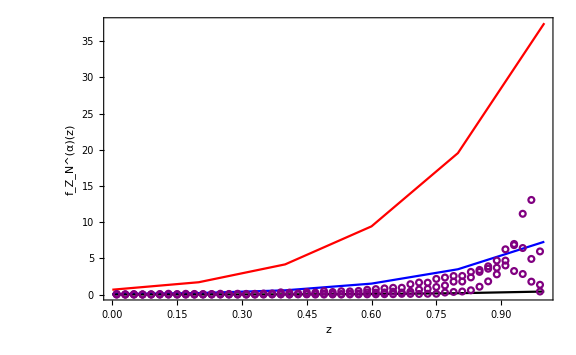

```mathematica
gStart=1; gEnd=3;
newMin=0.0; newMax=1;
legendCoord={0.85,0.75};

stringArray = Table[
(*"n="<>ToString [nArray[[t]]]*)
"θ="<>ToString [thetaArray[[t]]]
"n="<>ToString [nArray[[t]]]<>", θ="<>ToString [thetaArray[[t]]]<>", α="<>ToString[alphaArray[[t]]]
,{t,gStart,gEnd}];



gStart=Max[gStart,1]; gEnd=Min[gEnd,length];
legendPlotted=False;
oldMin=simDistArray[[All,1]]; oldMax=simDistArray[[All,2]];
newMin=Table[newMin,length];
newMax=Table[newMax,length];

plotArray=Table[
min=newMin[[t]];
max=newMax[[t]];
dx=simDistArray[[t,3]];
simDist=simDistArray[[t,4]];
hist=histArray[[t]];
color=colorArray[[t]];

thePlot=If[legendPlotted,
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color],
ListLinePlot[anaDataArray[[1;;Length[anaDataArray]-1,t]],ImageSize->Medium,PlotRange->All,PlotStyle->color,PlotLegends->Placed[LineLegend[colorArray[[gStart;;gEnd]],stringArray],legendCoord]]];

simDataPoints=Table[{x+dx/2,PDF[simDist,x+dx/2]},{x,min,max-dx/2,dx}];
simPlot=If[legendPlotted,
ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6]],
legendPlotted=True;ListPlot[simDataPoints,ImageSize->Medium,PlotRange->All,PlotMarkers->Graphics[{Purple,Thin,Circle[]},ImageSize->6],PlotLegends->Placed[{"Simulation"},legendCoord]]];

{thePlot,simPlot,hist,color},
{t,gStart,gEnd}];

Show[Flatten[{plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},PlotRangePadding->{{0},{0.0}},ImageSize->Large, Frame->True,FrameLabel->{{"f_Z_N^(α)(z)",None},{"z",None}}, FrameStyle->Directive[Automatic, 15, Bold]]
(*Frame labels
	FrameLabel->{{ToExpression["f_{Z_{N}}^\\alpha(z)", TeXForm],None},{"z",None}}
*)
(*Show[Flatten[{histArray[[All]],plotArray[[All,1]],plotArray[[All,2]]}],PlotRange->{{Min[newMin],Max[newMax]},All},ImageSize->Large]*)
```